```mathematica
Quit[]
```

# Effective Potential Finder

## Given a theory, it finds the thermal effective potential at one loop.

## Standard Model

## Define the DoF

### Gauge Sector

```mathematica
(*Group Theory Stuff*)
sigpauli1={{0,1},{1,0}};
sigpauli2={{0,-ⅈ},{ⅈ,0}};
sigpauli3={{1,0},{0,-1}};
eins={{1,0},{0,1}};
(*Gauge Fields*)
gaugefields={Subscript[W, 1],Subscript[W, 2],Subscript[W, 3],B};
cw=g/Sqrt[g^2+Subscript[g, w]^2];
sw=Subscript[g, w]/Sqrt[g^2+Subscript[g, w]^2];
Rot={{cw,-sw},{sw,cw}};
```

### Yukawa Sector

```mathematica
(*Quark weyl spinors*)
QLbar={Subscript[t̄, L],Subscript[b̄, L]};
QL={Subscript[t, L],Subscript[b, L]};
barfermfields={Subscript[t̄, L],Subscript[t̄, R],Subscript[b̄, L],Subscript[b̄, R]};
fermfields={Subscript[t, L],Subscript[t, R],Subscript[b, L],Subscript[b, R]};
Conjugate[Subscript[y, t]]^=Subscript[y, t];
Conjugate[Subscript[y, b]]^=Subscript[y, b];
```

### Scalar Sector

```mathematica
(*SU(2) Doublet*)
Phi={{1/Sqrt[2] (SuperPlus[G]+ⅈ*SuperMinus[G])},{1/Sqrt[2] (h+ⅈ*χ)}};
PhiHC=Conjugate[Transpose[Phi]];
Phiwig=(ⅈ sigpauli2.Conjugate[Phi]);
PhiwigHC=ConjugateTranspose[Phiwig];
(*Real Scalar Components*)
sfields={SuperPlus[G],SuperMinus[G],χ,h};
Conjugate[SuperPlus[G]]^=SuperPlus[G];
Conjugate[SuperMinus[G]]^=SuperMinus[G];
Conjugate[χ]^=χ;
Conjugate[h]^=h;
(*Unitary Condition*)
UnitG = {SuperPlus[G]->0,SuperMinus[G]->0,χ->0,h->v};
```

## Tree Level Potential

```mathematica
(*Creathe the V0*)
Vtree=Expand[-μ^2 PhiHC.Phi+λ(PhiHC.Phi)^2][[1,1]];
Vtree/.UnitG/.{v->h}
```

(h^4 λ)/4-(h^2 μ^2)/2

```mathematica
V0[h_]:=(h^4 λ)/4-(h^2 μ^2)/2
```

```mathematica
(*Find the VeV condition*)
Solve[D[V0[v],v]==0,μ]
```

{{μ→-v √λ},{μ→v √λ}}

```mathematica
VeV={μ->Sqrt[v^2*λ]};
```

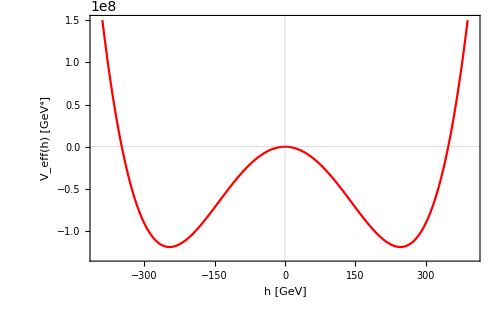

```mathematica
(*Plot the Veff*)
V0Plot = Plot[V0[h]/.{μ->88.565,λ->0.12938},{h,-400,400},
PlotTheme->"Scientific",
PlotRange->{{-400,400},{-1.3*10^8,1.5*10^8}},
PlotStyle->Directive[Red],
ImageSize->500,
PlotPoints->400,
BaseStyle->{FontSize->12},
FrameLabel->{Style[Row[{Style["h",Italic]," [","GeV","]"}],15],Style[Row[{Subscript[Style["V",Italic],"eff"],"(",Style["h",Italic],") [",Superscript["GeV","4"],"]"}],15]},LabelStyle->Directive[Black,12]
]
```

## Field Dependent Masses

### Scalars

```mathematica
(*Hessian Mass Matrix*)
MassMatrixScalars=Table[
D[D[Vtree,sfields[[i]]],sfields[[j]]],{i,4},{j,4}
];
(*Display the Matrix*)
MassMatrixScalars/.UnitG//MatrixForm
```

(v^2 λ-μ^2 | 0 | 0 | 0
0 | v^2 λ-μ^2 | 0 | 0
0 | 0 | v^2 λ-μ^2 | 0
0 | 0 | 0 | 3 v^2 λ-μ^2)

```mathematica
mG2[v_]:=v^2 λ-μ^2
mh2[v_]:=3 v^2 λ-μ^2
```

```mathematica
(*Just for funsies, we get the mass of the Higgs*)
MassMatrixScalars/.UnitG/.VeV//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2 v^2 λ)

### Gauge Sector

```mathematica
(*Gauge Mass Part of Kinetic Part*)
P=(ⅈ g (Subscript[W, 1] sigpauli1/2+Subscript[W, 2] sigpauli2/2+Subscript[W, 3] sigpauli3/2)+(ⅈ Subscript[g, w]/2) B eins).Phi[[1;;2,1]];
LGauge=Expand[ComplexExpand[Conjugate[P].P]];
LGauge/.UnitG
```

1/8 B^2 v^2 g_w^2+1/8 g^2 v^2 W_1^2+1/8 g^2 v^2 W_2^2-1/4 B g v^2 g_w W_3+1/8 g^2 v^2 W_3^2

```mathematica
(*Mass Matrix in Interaction Basis*)
MassGaugeMatrix=Table[If[i==j,2 Simplify[Coefficient[LGauge,gaugefields[[i]],2]],Simplify[Coefficient[Coefficient[LGauge,gaugefields[[i]]],gaugefields[[j]]]]],{i,4},{j,4}];

MassGaugeMatrix/.{SuperPlus[G]->0,SuperMinus[G]->0,χ->0,h->v}//MatrixForm

(*Masses of Physical Gauge Bosons*)
MG=MassGaugeMatrix/. UnitG;
NeutralBlock=MG[[3;;4,3;;4]];
NeutralPhys=Simplify[Rot.NeutralBlock.Transpose[Rot]];
MGPhys=MG;
MGPhys[[3;;4,3;;4]]=NeutralPhys;
MGPhys//MatrixForm
```

((g^2 v^2)/4 | 0 | 0 | 0
0 | (g^2 v^2)/4 | 0 | 0
0 | 0 | (g^2 v^2)/4 | -1/4 g v^2 g_w
0 | 0 | -1/4 g v^2 g_w | 1/4 v^2 g_w^2)

((g^2 v^2)/4 | 0 | 0 | 0
0 | (g^2 v^2)/4 | 0 | 0
0 | 0 | 1/4 v^2 (g^2+g_w^2) | 0
0 | 0 | 0 | 0)

```mathematica
mW2[v_]:=(g^2 v^2)/4
mZ2[v_]:=1/4 v^2 (g^2+Subscript[g, w]^2)
```

### Fermion Sector

```mathematica
Yuk1=Expand[-(Subscript[y, t] QLbar.Phiwig Subscript[t, R])[[1]]];
Yuk2=Expand[-(Subscript[y, t] PhiwigHC.QL Subscript[t̄, R])[[1]]];
Yuk=Yuk1+Yuk2;
Yuk/.UnitG
```

-(v t_R y_t (t̄)_L)/(√2)-(v t_L y_t (t̄)_R)/(√2)

```mathematica
(*Mass Matrix in Chyral Basis*)
MassFermMatrix=Table[Coefficient[Coefficient[-(Yuk1+Yuk2),barfermfields[[i]]],fermfields[[j]]],{i,2},{j,2}];
MatrixForm[MassFermMatrix/.UnitG]
```

(0 | (v y_t)/(√2)
(v y_t)/(√2) | 0)

```mathematica
mt2[v_]:=((v Subscript[y, t])/(√2))^2
```

## Coleman Weinberg

#### MSbar

```mathematica
VCWi[m2_,n_,c_,ρ_]:=(n/(64*π^2))*m2^2*(Log[m2/ρ^2]-c)
VCW[h_,ρ_]:=VCWi[mG2[h],3,3/2,ρ]+VCWi[mh2[h],1,3/2,ρ]+VCWi[mW2[h],6,5/6,ρ]+VCWi[mZ2[h],3,5/6,ρ]+VCWi[mt2[h],-12,3/2,ρ]
VCW[h,ρ]
```

(3 g^4 h^4 (-5/6+Log[(g^2 h^2)/(4 ρ^2)]))/(512 π^2)+(3 (h^2 λ-μ^2)^2 (-3/2+Log[(h^2 λ-μ^2)/ρ^2]))/(64 π^2)+((3 h^2 λ-μ^2)^2 (-3/2+Log[(3 h^2 λ-μ^2)/ρ^2]))/(64 π^2)+(3 h^4 (-5/6+Log[(h^2 (g^2+g_w^2))/(4 ρ^2)]) (g^2+g_w^2)^2)/(1024 π^2)-(3 h^4 (-3/2+Log[(h^2 y_t^2)/(2 ρ^2)]) y_t^4)/(64 π^2)

```mathematica
VCWN[h_,ρ_]:=(3 g^4 h^4 (-5/6+Log[(g^2 h^2)/(4 ρ^2)]))/(512 π^2)+(3 (h^2 λ-μ^2)^2 (-3/2+Log[(h^2 λ-μ^2)/ρ^2]))/(64 π^2)+((3 h^2 λ-μ^2)^2 (-3/2+Log[(3 h^2 λ-μ^2)/ρ^2]))/(64 π^2)+(3 h^4 (-5/6+Log[(h^2 (g^2+gw^2))/(4 ρ^2)]) (g^2+gw^2)^2)/(1024 π^2)-(3 h^4 (-3/2+Log[(h^2 Subscript[y, t]^2)/(2 ρ^2)]) Subscript[y, t]^4)/(64 π^2)
VCWNG[h_,ρ_]:=(3 g^4 h^4 (-5/6+Log[(g^2 h^2)/(4 ρ^2)]))/(512 π^2)+((3 h^2 λ-μ^2)^2 (-3/2+Log[(3 h^2 λ-μ^2)/ρ^2]))/(64 π^2)+(3 h^4 (-5/6+Log[(h^2 (g^2+gw^2))/(4 ρ^2)]) (g^2+gw^2)^2)/(1024 π^2)-(3 h^4 (-3/2+Log[(h^2 Subscript[y, t]^2)/(2 ρ^2)]) Subscript[y, t]^4)/(64 π^2)
```

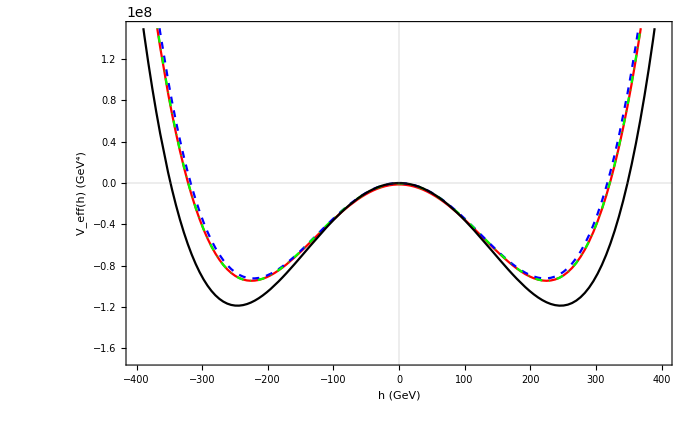

```mathematica
(*Plot the Veff*)
V0Plot = Plot[{V0[h]+Re[VCWN[h,246.22]]/.{μ->88.565,λ->0.12938,g->0.65288,gw->0.34979,Subscript[y, t]->0.93351},V0[h]+Re[-(3 h^4 (-3/2+Log[(h^2 Subscript[y, t]^2)/(2 ρ^2)]) Subscript[y, t]^4)/(64 π^2)]/.{μ->88.565,ρ->246.22,λ->0.12938,Subscript[y, t]->0.93351},V0[h]+Re[VCWNG[h,246.22]]/.{μ->88.565,λ->0.12938,g->0.65288,gw->0.34979,Subscript[y, t]->0.93351,ρ->246.22},V0[h]/.{μ->88.565,λ->0.12938}},{h,-400,400},
PlotTheme->"Scientific",
PlotRange->{{-400,400},{-1.7*10^8,1.5*10^8}},
PlotStyle->{Directive[Red],Directive[Blue,Dashed],Directive[Green,DotDashed],Directive[Black]},
ImageSize->700,PlotPoints->3,
BaseStyle->{FontSize->12},
FrameLabel->{Style[Row[{Style["h",Italic]," (","GeV",")"}],15],Style[Row[{Subscript[Style["V",Italic],"eff"],"(",Style["h",Italic],") (",Superscript["GeV","4"],")"}],15]},LabelStyle->Directive[Black,12]
]
```

#### On-Shell

```mathematica
VOSi[m2_,m02_,d_]:=d/(64*π^2)*(m2^2*(Log[m2/m02]-3/2)+2*m2*m02)
VOS[h_]:=VOSi[mh2[h],mh2[μ/(√λ)],1]+VOSi[mW2[h],mW2[μ/(√λ)],6]+VOSi[mZ2[h],mZ2[μ/(√λ)],3]+VOSi[mt2[h],mt2[μ/(√λ)],-12]
VOS[h]
```

(3 ((g^4 h^2 μ^2)/(8 λ)+1/16 g^4 h^4 (-3/2+Log[(h^2 λ)/μ^2])))/(32 π^2)+(4 μ^2 (3 h^2 λ-μ^2)+(3 h^2 λ-μ^2)^2 (-3/2+Log[(3 h^2 λ-μ^2)/(2 μ^2)]))/(64 π^2)+(3 ((h^2 μ^2 (g^2+g_w^2)^2)/(8 λ)+1/16 h^4 (-3/2+Log[(h^2 λ)/μ^2]) (g^2+g_w^2)^2))/(64 π^2)-(3 ((h^2 μ^2 y_t^4)/(2 λ)+1/4 h^4 (-3/2+Log[(h^2 λ)/μ^2]) y_t^4))/(16 π^2)

```mathematica
VOSN[h_]:=(3 ((g^4 h^2 μ^2)/(8 λ)+1/16 g^4 h^4 (-3/2+Log[(h^2 λ)/μ^2])))/(32 π^2)+(4 μ^2 (3 h^2 λ-μ^2)+(3 h^2 λ-μ^2)^2 (-3/2+Log[(3 h^2 λ-μ^2)/(2 μ^2)]))/(64 π^2)+(3 ((h^2 μ^2 (g^2+gw^2)^2)/(8 λ)+1/16 h^4 (-3/2+Log[(h^2 λ)/μ^2]) (g^2+gw^2)^2))/(64 π^2)-(3 ((h^2 μ^2 Subscript[y, t]^4)/(2 λ)+1/4 h^4 (-3/2+Log[(h^2 λ)/μ^2]) Subscript[y, t]^4))/(16 π^2)
```

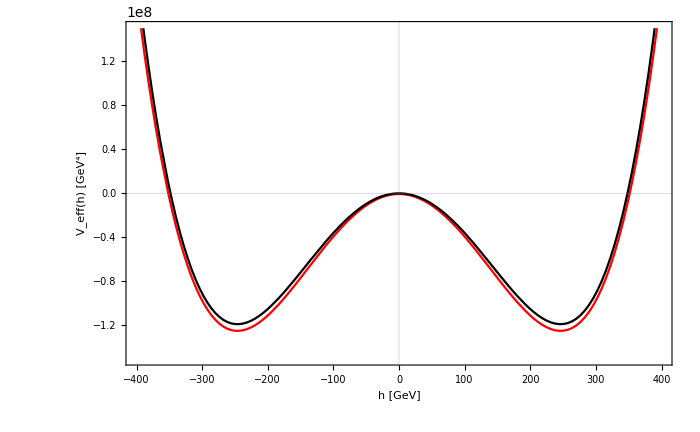

```mathematica
(*Plot the Veff*)
V0Plot = Plot[{V0[h]+Re[VOSN[h]]/.{μ->88.565,λ->0.12938,g->0.65288,gw->0.34979,Subscript[y, t]->0.93351},V0[h]/.{μ->88.565,λ->0.12938}},{h,-400,400},
PlotTheme->"Scientific",
PlotRange->{{-400,400},{-1.5*10^8,1.5*10^8}},
PlotStyle->{Directive[Red],Directive[Black]},
ImageSize->700,PlotPoints->3,
BaseStyle->{FontSize->12},
FrameLabel->{Style[Row[{Style["h",Italic]," [","GeV","]"}],15],Style[Row[{Subscript[Style["V",Italic],"eff"],"(",Style["h",Italic],") [",Superscript["GeV","4"],"]"}],15]},LabelStyle->Directive[Black,12]
]
```

```mathematica
params={μ->88.565,λ->0.12938,g->0.65288,gw->0.34979,Subscript[y,t]->0.93351};
v=88.565/Sqrt[0.12938]; (* ≈246 GeV*)
Veff[h_]:=V0[h]+Re[VOSN[h]]/. params;

(*Should both be≈0*)
D[VOSN[h],h]/. h->v/. params
D[VOSN[h],{h,2}]/. h->v/. params
```

-7.29837×10^-11

-4.31958×10^-15